```mathematica
radc2[ξ_]=(rc)^2*(1+ξ)/(1-ξ)
radb2[ξ_]=(rb)^2*(1+ξ)/(1-ξ)
```

(rc^2 (1+ξ))/(1-ξ)

(rb^2 (1+ξ))/(1-ξ)

```mathematica
o[ξ_]=Sqrt[1-x]*((1-ξ)/2)^(3/4)*Sqrt[(rc)^3*(x)/(1-x)((1-ξ)/2)^(-3/2)*(1/(1+radc2[ξ]))^(3/2)+(rb)^3*(1/q-1)((1-ξ)/2)^(-3/2)*(1/(1+radb2[ξ]))^(3/2)+1-ϵ*(1/((1-x)^(2/3)))]
```

(√(1-x) (1-ξ)^(3/4) √(1-ϵ/(1-x)^(2/3)+(2 √2 (-1+1/q) rb^3 (1/(1+(rb^2 (1+ξ))/(1-ξ)))^(3/2))/(1-ξ)^(3/2)+(2 √2 rc^3 x (1/(1+(rc^2 (1+ξ))/(1-ξ)))^(3/2))/((1-x) (1-ξ)^(3/2))))/2^(3/4)

```mathematica
D[o[ξ],ξ]//Simplify
```

(√(1-x) (-3+(3 ϵ)/(1-x)^(2/3)+(12 (-1+q) rb^5 √((2-2 ξ)/(1-ξ+rb^2 (1+ξ))))/(q √(1-ξ) (1-ξ+rb^2 (1+ξ))^2)+(12 rc^5 x √((2-2 ξ)/(1-ξ+rc^2 (1+ξ))))/((-1+x) √(1-ξ) (1-ξ+rc^2 (1+ξ))^2)))/(4 2^(3/4) (1-ξ)^(1/4) √(1-ϵ/(1-x)^(2/3)+(2 √2 (-1+1/q) rb^3 (1/(1-(rb^2 (1+ξ))/(-1+ξ)))^(3/2))/(1-ξ)^(3/2)+(2 √2 rc^3 x (1/(1-(rc^2 (1+ξ))/(-1+ξ)))^(3/2))/((1-x) (1-ξ)^(3/2))))

```mathematica
D[o[ξ],ξ]/.ξ->0.6/.rc->10/.rb->1/.x->0.9/.q->0.9/.ϵ->0.1
```

-0.794838

```mathematica
NumberForm[-2.513499662471393,16]
```

-2.513499662471393

```mathematica
((o[0.6+0.0001]/.rc->10/.rb->1/.x->0.9/.q->0.9/.ϵ->0.1)-(o[0.6-0.0001]/.rc->10/.rb->1/.x->0.9/.q->0.9/.ϵ->0.1))/(2*0.0001)
```

-0.794838

```mathematica
NumberForm[-2.5134996727338432,16]
```

-2.513499672733843

```mathematica
o[0.6]/.rc->10/.rb->1/.x->0.9/.q->0.9/.ϵ->0.1
```

0.343316

```mathematica
NumberForm[0.7492798887684391,16]
```

0.749279888768439

```mathematica
rad[ξ_]:=Sqrt[(1+ξ)/(1-ξ)]
```

```mathematica
radc2[ξ_,r_]:=(r)^2*(1+ξ)/(1-ξ);
omega[ξ_,x_,q_,r_,ϵ_]:=((1-ξ)/2)^(3/4)*Sqrt[(r)^3*(x)/(1-x)((1-ξ)/2)^(-3/2)*(1/(1+radc2[ξ,r]))^(3/2)+1/q-ϵ*(1/((1-x)^(2/3)))]
```

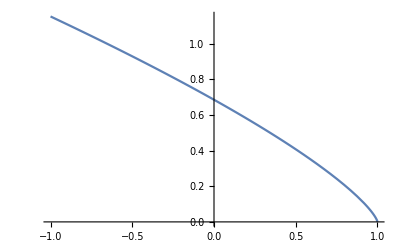

```mathematica
ϵ=0.1;r=10;
q=0.7;
x=0;
Plot[omega[ξ,x,q,r,ϵ],{ξ,-1,1}]
```

```mathematica
domegadxi[ξ_,x_,q_,r_,ϵ_]:=-((3 ((-1+x+q (1-x)^(1/3) ϵ) (1-ξ)^(5/2)+r^4 (-1+x+q (1-x)^(1/3) ϵ) √(1-ξ) (1+ξ)^2-2 r^2 (-1+x+q (1-x)^(1/3) ϵ) √(1-ξ) (-1+ξ^2)-4 q r^5 x √((2-2 ξ)/(1-ξ+r^2 (1+ξ)))))/(4 q (-1+x) (2-2 ξ)^(3/4) (1-ξ+r^2 (1+ξ))^2 √(1/q-ϵ/(1-x)^(2/3)-(r^3 x ((2-2 ξ)/(1-ξ+r^2 (1+ξ)))^(3/2))/((-1+x) (1-ξ)^(3/2)))))
```

```mathematica
kappa2[ξ_,x_,q_,r_,ϵ_]:=4*omega[ξ,x,q,r,ϵ]^2*(1+((1+ξ)(1-ξ))/(2*omega[ξ,x,q,r,ϵ])*domegadxi[ξ,x,q,r,ϵ])
```

```mathematica
kappa[ξ_,x_,q_,r_,ϵ_]:=Sqrt[kappa2[ξ,x,q,r,ϵ]]
```

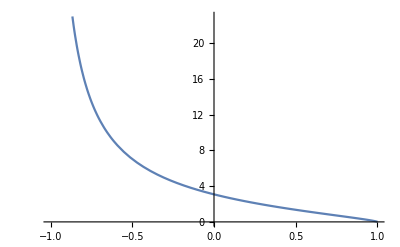

```mathematica
ϵ=0.1;r=10;
q=1.1;
x=0.9;
Plot[kappa[ξ,x,q,r,ϵ],{ξ,-1,1}]
```

```mathematica
omegaMinusHalfKappa[ξ_,x_,q_,r_,ϵ_]:=omega[ξ,x,q,r,ϵ]-kappa[ξ,x,q,r,ϵ]/2
```

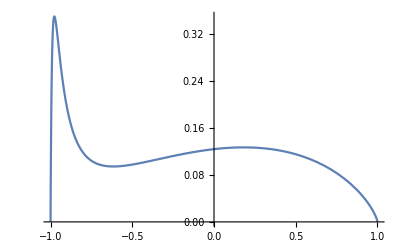

```mathematica
ϵ=0.1;r=10;
q=1;
x=0.01;
Plot[omegaMinusHalfKappa[ξ,x,q,r,ϵ],{ξ,-1,1},PlotRange->All]
```

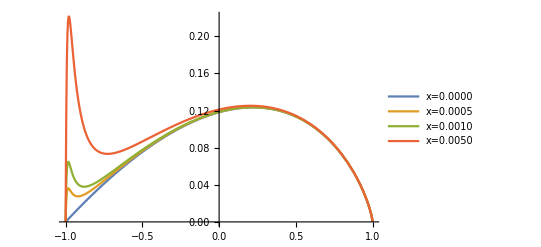

```mathematica
ϵ=0.1;r=10;
q=1;
Plot[{omegaMinusHalfKappa[ξ,0,q,r,ϵ],omegaMinusHalfKappa[ξ,0.0005,q,r,ϵ],omegaMinusHalfKappa[ξ,0.001,q,r,ϵ],omegaMinusHalfKappa[ξ,0.005,q,r,ϵ](*,omegaMinusHalfKappa[ξ,0.01,q,r,ϵ],omegaMinusHalfKappa[ξ,0.05,q,r,ϵ],omegaMinusHalfKappa[ξ,0.1,q,r,ϵ]*)},{ξ,-1,1},PlotRange->All,PlotLegends->{"x=0.0000","x=0.0005","x=0.0010","x=0.0050"}]
```

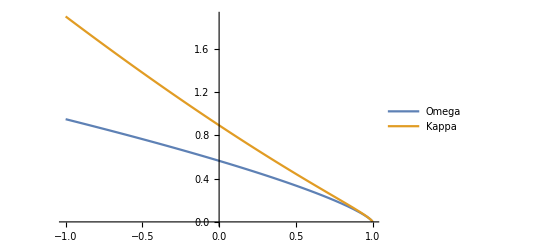

```mathematica
ϵ=0.1;r=10;
q=1;
x=0;
Plot[{omega[ξ,x,q,r,ϵ],kappa[ξ,x,q,r,ϵ]},{ξ,-1,1},PlotLegends->{"Omega","Kappa"}]
```

-Graphics3D-

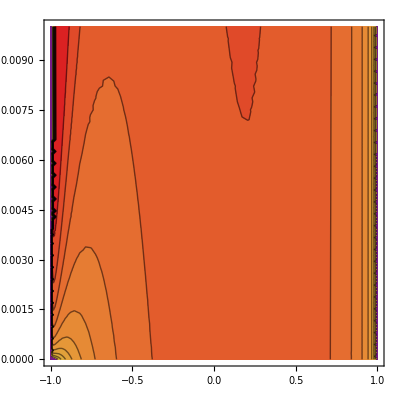

```mathematica
ϵ=0.1;r=10;
q=1;
Plot3D[omegaMinusHalfKappa[ξ,x,q,r,ϵ],{ξ,-1,1},{x,0,0.01},PlotRange->All,ColorFunction->"Rainbow"]
ContourPlot[Log10[omegaMinusHalfKappa[ξ,x,q,r,ϵ]],{ξ,-1,1},{x,0,0.01},PlotRange->All,Contours->10,ColorFunction->"Rainbow"]
```